```mathematica
Clear[count]
```

```mathematica
Allimages = {};
concentrations = {1,2.5,5,10,17.5,25,50,100};
Do[
positions = Flatten[Table[{( x-1)20+15,( y-1)20+15},{y,1,6},{x,1,6}],1];
Do[AppendTo[positions,{64+i,64}];AppendTo[positions,{64,64+i}];,{i,-10,10,4}];
imout=RandomVariate[NormalDistribution[500,100],{128,128}];
Do[imout[[x,y]] += N[400 E^(-(x-x0)^2/(2 σ^2))E^(-(y-y0)^2/(2 σ^2))/.x0->(positions[[i,1]])/.y0->(positions[[i,2]])/.σ->N[Sqrt[10/π]]],{i,1,Length[positions]},{x,Max[Round[(positions[[i,1]])-6],1],Min[Round[(positions[[i,1]])+6],256]},{y,Max[Round[(positions[[i,2]])-6],1],Min[Round[(positions[[i,2]])+6],128]}];
im1 =  Image[imout/2^16];
numparticles =Round[N[36 concentrations[[count]]/(10+concentrations[[count]])]];
positions = RandomSample[Flatten[Table[{( x-1)20+15,( y-1)20+15},{y,1,6},{x,1,6}],1],numparticles];
Do[AppendTo[positions,{64+i,64}];AppendTo[positions,{64,64+i}];,{i,-10,10,4}];
imout=RandomVariate[NormalDistribution[500+2 concentrations[[count]],100],{128,128}];
Do[imout[[x,y]] += N[400 E^(-(x-x0)^2/(2 σ^2))E^(-(y-y0)^2/(2 σ^2))/.x0->(positions[[i,1]])/.y0->(positions[[i,2]])/.σ->N[Sqrt[10/π]]],{i,1,Length[positions]},{x,Max[Round[(positions[[i,1]])-6],1],Min[Round[(positions[[i,1]])+6],256]},{y,Max[Round[(positions[[i,2]])-6],1],Min[Round[(positions[[i,2]])+6],128]}];
im2 =  Image[imout/2^16];
toout = {im1,im2};
Export["C:\\Users\\jameswa\\Documents\\GitHub\\JIM-Immobilized-Microscopy-Suite\\Jim_v5_8\\Example_Data\\Tutorial_5_Kd_Single_Binding_Site_Substrate\\"~~ToString[count]~~"_"~~ToString[concentrations[[count]]]~~"nM.tiff",toout];
AppendTo[Allimages,ImageAdjust[#]&/@toout];,{count,1,Length[concentrations]}]
```

```mathematica
toout
```

{-Graphics-,-Graphics-}

```mathematica
Allimages[[All,2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

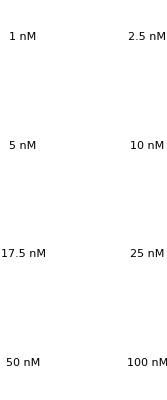

```mathematica
toout = GraphicsGrid[Partition[Table[Labeled[GraphicsRow[Allimages[[i]]],Style[ToString[concentrations[[i]]]~~" nM",{FontFamily->"Times",FontSize->20, Bold}],{Top}],{i,1,Length[concentrations]}],2],Spacings->{30,-50}]
```

```mathematica
Export["C:\\Users\\jameswa\\Documents\\GitHub\\JIM-Immobilized-Microscopy-Suite\\Jim_v5_8\\Example_Data\\Tutorial_5_Kd_Single_Binding_Site_Substrate\\compiled.jpeg",toout,ImageResolution->500]
```

C:\Users\jameswa\Documents\GitHub\JIM-Immobilized-Microscopy-Suite\Jim_v5_8\Example_Data\Tutorial_5_Kd_Single_Binding_Site_Substrate\compiled.jpeg